# Achieving a Performance Target

## Supplemental material for Sec. 9.

```mathematica
?InverseCDF
```

```mathematica
T=1;r=0.02;
```

```mathematica
y[W_,t_]:=InverseCDF[NormalDistribution[0,1],ⅇ^(r(T-t))W]
```

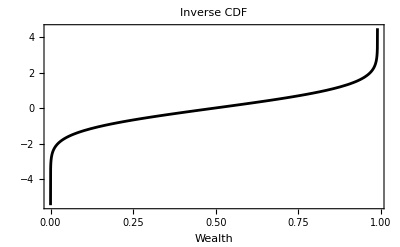

```mathematica
browneInverseCDFPlot=Plot[y[W,#1],{W,0,1},
PlotRange->{All,All},
PlotLabel->Style["Inverse CDF",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Wealth",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->Black
]&[0.5,r]
```

```mathematica
σ=1;
```

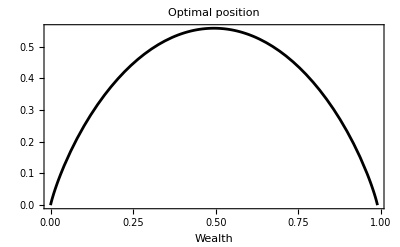

```mathematica
browneOptimalPositionPlot=Plot[1/Sqrt[2π σ^2(T-#)] Exp[-1/2 y[W,#]^2-r(T-#)],{W,0,1},
PlotRange->{All,All},
PlotLabel->Style[
"Optimal position",
FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Wealth",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->Black
]&@0.5
```

```mathematica
a=0.10;
```

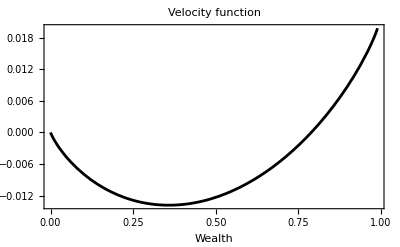

```mathematica
browneVelocityFunctionPlot=Plot[
r W-((a-r)/2)/Sqrt[2π σ^2(T-#)] Exp[-1/2 y[W,#]^2-r(T-#)],{W,0,1},
PlotRange->{All,All},
PlotLabel->Style["Velocity function",FontSize->13,FontColor->Black],
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Wealth",FontSize->12]},
FrameStyle->Directive[Black,12],
PlotStyle->Black]&@0.5
```

```mathematica
writeDirectory=NotebookDirectory[]<>"/output/browne";
```

```mathematica
SetDirectory@writeDirectory
```

```mathematica
Export["browneInverseCDFPlot.pdf",browneInverseCDFPlot]
```

browneInverseCDFPlot.pdf

```mathematica
Export["browneOptimalPositionPlot.pdf",browneOptimalPositionPlot]
```

browneOptimalPositionPlot.pdf

```mathematica
Export["browneVelocityFunctionPlot.pdf",browneVelocityFunctionPlot]
```

browneVelocityFunctionPlot.pdf